## 4th Assignment: Stochastic FEM F. I. Giasemis

### FEM

#### The stiffness matrix for one element

```mathematica
aelem=0.05;
belem=0.05;
ν=0.3;
t=0.2;
r=aelem/belem;
ρ=(1-ν)/2;
μ=3(1+ν)/2;
λ=3(1-3ν)/2;

kinput=t /(12(1-ν^2)){{4/r+4 ρ r,0,0,0,0,0,0,0},{μ,4r+4ρ/r,0,0,0,0,0,0},{-4/r+2 ρ r,λ,4/r+4 ρ r,0,0,0,0,0},{-λ,2r-4ρ/r,-μ,4r+4ρ/r,0,0,0,0},{-2/r-2ρ r,-μ,2/r-4ρ r,λ,4/r+4ρ r,0,0,0},{-μ,-2r-2ρ/r,-λ,-4r+2ρ/r,μ,4r+4ρ/r,0,0},{2/r-4ρ r,-λ,-2/r-2 ρ r,μ,-4/r+2 ρ r,λ,4/r+4 ρ r,0},{λ,-4r+2ρ/r,μ,-2r-2ρ/r,-λ,2r-4ρ/r,-μ,4r+4ρ/r}};
k=kinput+Transpose[kinput]-DiagonalMatrix[{kinput[[1,1]],kinput[[1,1]],kinput[[1,1]],kinput[[1,1]],kinput[[1,1]],kinput[[1,1]],kinput[[1,1]],kinput[[1,1]]}];

klocal[x_]:=(
EY=f[x];
Return[EY k])
```

#### Assembling the global stiffness matrix

```mathematica
dim=(40+1) (10+1) 2;
global[i_,j_,m_,n_]:=(
x=Mod[i,41] 2aelem-aelem;
kglobal=ConstantArray[0,{dim,dim}];
kglobal[[2 i-1,2 i-1]]+=klocal[x][[1,1]];
kglobal[[2 i-1,2 i]]+=klocal[x][[1,2]];
kglobal[[2 i-1,2 j-1]]+=klocal[x][[1,3]];
kglobal[[2 i-1,2 j]]+=klocal[x][[1,4]];
kglobal[[2 i-1,2 m-1]]+=klocal[x][[1,5]];
kglobal[[2 i-1,2 m]]+=klocal[x][[1,6]];
kglobal[[2 i-1,2 n-1]]+=klocal[x][[1,7]];
kglobal[[2 i-1,2 n]]+=klocal[x][[1,8]];
kglobal[[2 i,2 i-1]]+=klocal[x][[2,1]];
kglobal[[2 i,2 i]]+=klocal[x][[2,2]];
kglobal[[2 i,2 j-1]]+=klocal[x][[2,3]];
kglobal[[2 i,2 j]]+=klocal[x][[2,4]];
kglobal[[2 i,2 m-1]]+=klocal[x][[2,5]];
kglobal[[2 i,2 m]]+=klocal[x][[2,6]];
kglobal[[2 i,2 n-1]]+=klocal[x][[2,7]];
kglobal[[2 i,2 n]]+=klocal[x][[2,8]];
kglobal[[2 j-1,2 i-1]]+=klocal[x][[3,1]];
kglobal[[2 j-1,2 i]]+=klocal[x][[3,2]];
kglobal[[2 j-1,2 j-1]]+=klocal[x][[3,3]];
kglobal[[2 j-1,2 j]]+=klocal[x][[3,4]];
kglobal[[2 j-1,2 m-1]]+=klocal[x][[3,5]];
kglobal[[2 j-1,2 m]]+=klocal[x][[3,6]];
kglobal[[2 j-1,2 n-1]]+=klocal[x][[3,7]];
kglobal[[2 j-1,2 n]]+=klocal[x][[3,8]];
kglobal[[2 j,2 i-1]]+=klocal[x][[4,1]];
kglobal[[2 j,2 i]]+=klocal[x][[4,2]];
kglobal[[2 j,2 j-1]]+=klocal[x][[4,3]];
kglobal[[2 j,2 j]]+=klocal[x][[4,4]];
kglobal[[2 j,2 m-1]]+=klocal[x][[4,5]];
kglobal[[2 j,2 m]]+=klocal[x][[4,6]];
kglobal[[2 j,2 n-1]]+=klocal[x][[4,7]];
kglobal[[2 j,2 n]]+=klocal[x][[4,8]];
kglobal[[2 m-1,2 i-1]]+=klocal[x][[5,1]];
kglobal[[2 m-1,2 i]]+=klocal[x][[5,2]];
kglobal[[2 m-1,2 j-1]]+=klocal[x][[5,3]];
kglobal[[2 m-1,2 j]]+=klocal[x][[5,4]];
kglobal[[2 m-1,2 m-1]]+=klocal[x][[5,5]];
kglobal[[2 m-1,2 m]]+=klocal[x][[5,6]];
kglobal[[2 m-1,2 n-1]]+=klocal[x][[5,7]];
kglobal[[2 m-1,2 n]]+=klocal[x][[5,8]];
kglobal[[2 m,2 i-1]]+=klocal[x][[6,1]];
kglobal[[2 m,2 i]]+=klocal[x][[6,2]];
kglobal[[2 m,2 j-1]]+=klocal[x][[6,3]];
kglobal[[2 m,2 j]]+=klocal[x][[6,4]];
kglobal[[2 m,2 m-1]]+=klocal[x][[6,5]];
kglobal[[2 m,2 m]]+=klocal[x][[6,6]];
kglobal[[2 m,2 n-1]]+=klocal[x][[6,7]];
kglobal[[2 m,2 n]]+=klocal[x][[6,8]];
kglobal[[2 n-1,2 i-1]]+=klocal[x][[7,1]];
kglobal[[2 n-1,2 i]]+=klocal[x][[7,2]];
kglobal[[2 n-1,2 j-1]]+=klocal[x][[7,3]];
kglobal[[2 n-1,2 j]]+=klocal[x][[7,4]];
kglobal[[2 n-1,2 m-1]]+=klocal[x][[7,5]];
kglobal[[2 n-1,2 m]]+=klocal[x][[7,6]];
kglobal[[2 n-1,2 n-1]]+=klocal[x][[7,7]];
kglobal[[2 n-1,2 n]]+=klocal[x][[7,8]];
kglobal[[2 n,2 i-1]]+=klocal[x][[8,1]];
kglobal[[2 n,2 i]]+=klocal[x][[8,2]];
kglobal[[2 n,2 j-1]]+=klocal[x][[8,3]];
kglobal[[2 n,2 j]]+=klocal[x][[8,4]];
kglobal[[2 n,2 m-1]]+=klocal[x][[8,5]];
kglobal[[2 n,2 m]]+=klocal[x][[8,6]];
kglobal[[2 n,2 n-1]]+=klocal[x][[8,7]];
kglobal[[2 n,2 n]]+=klocal[x][[8,8]];
Return[kglobal])
```

#### The global stiffness matrix

```mathematica
Kglobal:=(
Kglobal= ConstantArray[0,{dim,dim}];
For[index =0,index≤408,index+=1,
i=1+index;
j=2+index;
m=43+index;
n=42+index;
If[Divisible[i,41]==False, Kglobal+=global[i,j,m,n]]
];
Return[Kglobal])
```

#### Boundary conditions

```mathematica
fix[x_]:=(
For[i=1,i≤dim,i+=1,
KGLOBAL[[x,i]]=0;
KGLOBAL[[i,x]]=0;];
KGLOBAL[[x,x]]=10^10;)
```

```mathematica
fixall:=(
For[x=1,x≤821,x+=82,
fix[x]];
For[x=2,x≤822,x+=82,
fix[x]];)
```

#### Solve the system

```mathematica
aelem=0.05;
belem=0.05;
ν=0.3;
t=0.2;
r=aelem/belem;
ρ=(1-ν)/2;
μ=3(1+ν)/2;
λ=3(1-3ν)/2;
dim=(40+1) (10+1) 2;

global[i_,j_,m_,n_]:=(
x=Mod[i,41] 2aelem-aelem;
kglobal=ConstantArray[0,{dim,dim}];
kglobal[[2 i-1,2 i-1]]+=klocal[x][[1,1]];
kglobal[[2 i-1,2 i]]+=klocal[x][[1,2]];
kglobal[[2 i-1,2 j-1]]+=klocal[x][[1,3]];
kglobal[[2 i-1,2 j]]+=klocal[x][[1,4]];
kglobal[[2 i-1,2 m-1]]+=klocal[x][[1,5]];
kglobal[[2 i-1,2 m]]+=klocal[x][[1,6]];
kglobal[[2 i-1,2 n-1]]+=klocal[x][[1,7]];
kglobal[[2 i-1,2 n]]+=klocal[x][[1,8]];
kglobal[[2 i,2 i-1]]+=klocal[x][[2,1]];
kglobal[[2 i,2 i]]+=klocal[x][[2,2]];
kglobal[[2 i,2 j-1]]+=klocal[x][[2,3]];
kglobal[[2 i,2 j]]+=klocal[x][[2,4]];
kglobal[[2 i,2 m-1]]+=klocal[x][[2,5]];
kglobal[[2 i,2 m]]+=klocal[x][[2,6]];
kglobal[[2 i,2 n-1]]+=klocal[x][[2,7]];
kglobal[[2 i,2 n]]+=klocal[x][[2,8]];
kglobal[[2 j-1,2 i-1]]+=klocal[x][[3,1]];
kglobal[[2 j-1,2 i]]+=klocal[x][[3,2]];
kglobal[[2 j-1,2 j-1]]+=klocal[x][[3,3]];
kglobal[[2 j-1,2 j]]+=klocal[x][[3,4]];
kglobal[[2 j-1,2 m-1]]+=klocal[x][[3,5]];
kglobal[[2 j-1,2 m]]+=klocal[x][[3,6]];
kglobal[[2 j-1,2 n-1]]+=klocal[x][[3,7]];
kglobal[[2 j-1,2 n]]+=klocal[x][[3,8]];
kglobal[[2 j,2 i-1]]+=klocal[x][[4,1]];
kglobal[[2 j,2 i]]+=klocal[x][[4,2]];
kglobal[[2 j,2 j-1]]+=klocal[x][[4,3]];
kglobal[[2 j,2 j]]+=klocal[x][[4,4]];
kglobal[[2 j,2 m-1]]+=klocal[x][[4,5]];
kglobal[[2 j,2 m]]+=klocal[x][[4,6]];
kglobal[[2 j,2 n-1]]+=klocal[x][[4,7]];
kglobal[[2 j,2 n]]+=klocal[x][[4,8]];
kglobal[[2 m-1,2 i-1]]+=klocal[x][[5,1]];
kglobal[[2 m-1,2 i]]+=klocal[x][[5,2]];
kglobal[[2 m-1,2 j-1]]+=klocal[x][[5,3]];
kglobal[[2 m-1,2 j]]+=klocal[x][[5,4]];
kglobal[[2 m-1,2 m-1]]+=klocal[x][[5,5]];
kglobal[[2 m-1,2 m]]+=klocal[x][[5,6]];
kglobal[[2 m-1,2 n-1]]+=klocal[x][[5,7]];
kglobal[[2 m-1,2 n]]+=klocal[x][[5,8]];
kglobal[[2 m,2 i-1]]+=klocal[x][[6,1]];
kglobal[[2 m,2 i]]+=klocal[x][[6,2]];
kglobal[[2 m,2 j-1]]+=klocal[x][[6,3]];
kglobal[[2 m,2 j]]+=klocal[x][[6,4]];
kglobal[[2 m,2 m-1]]+=klocal[x][[6,5]];
kglobal[[2 m,2 m]]+=klocal[x][[6,6]];
kglobal[[2 m,2 n-1]]+=klocal[x][[6,7]];
kglobal[[2 m,2 n]]+=klocal[x][[6,8]];
kglobal[[2 n-1,2 i-1]]+=klocal[x][[7,1]];
kglobal[[2 n-1,2 i]]+=klocal[x][[7,2]];
kglobal[[2 n-1,2 j-1]]+=klocal[x][[7,3]];
kglobal[[2 n-1,2 j]]+=klocal[x][[7,4]];
kglobal[[2 n-1,2 m-1]]+=klocal[x][[7,5]];
kglobal[[2 n-1,2 m]]+=klocal[x][[7,6]];
kglobal[[2 n-1,2 n-1]]+=klocal[x][[7,7]];
kglobal[[2 n-1,2 n]]+=klocal[x][[7,8]];
kglobal[[2 n,2 i-1]]+=klocal[x][[8,1]];
kglobal[[2 n,2 i]]+=klocal[x][[8,2]];
kglobal[[2 n,2 j-1]]+=klocal[x][[8,3]];
kglobal[[2 n,2 j]]+=klocal[x][[8,4]];
kglobal[[2 n,2 m-1]]+=klocal[x][[8,5]];
kglobal[[2 n,2 m]]+=klocal[x][[8,6]];
kglobal[[2 n,2 n-1]]+=klocal[x][[8,7]];
kglobal[[2 n,2 n]]+=klocal[x][[8,8]];
Return[kglobal]);


kinput=t /(12(1-ν^2)){{4/r+4 ρ r,0,0,0,0,0,0,0},{μ,4r+4ρ/r,0,0,0,0,0,0},{-4/r+2 ρ r,λ,4/r+4 ρ r,0,0,0,0,0},{-λ,2r-4ρ/r,-μ,4r+4ρ/r,0,0,0,0},{-2/r-2ρ r,-μ,2/r-4ρ r,λ,4/r+4ρ r,0,0,0},{-μ,-2r-2ρ/r,-λ,-4r+2ρ/r,μ,4r+4ρ/r,0,0},{2/r-4ρ r,-λ,-2/r-2 ρ r,μ,-4/r+2 ρ r,λ,4/r+4 ρ r,0},{λ,-4r+2ρ/r,μ,-2r-2ρ/r,-λ,2r-4ρ/r,-μ,4r+4ρ/r}};
k=kinput+Transpose[kinput]-DiagonalMatrix[{kinput[[1,1]],kinput[[1,1]],kinput[[1,1]],kinput[[1,1]],kinput[[1,1]],kinput[[1,1]],kinput[[1,1]],kinput[[1,1]]}];

F=ConstantArray[0,dim];
F[[dim]] = -10;




U[y_]:=(

EY=y;

klocal[x_]:=EY k;

Kglobal= ConstantArray[0,{dim,dim}];
For[index =0,index≤408,index+=1,
i=1+index;
j=2+index;
m=43+index;
n=42+index;
If[Divisible[i,41]==False, Kglobal+=global[i,j,m,n]]
];

KGLOBAL=Kglobal;

fixall;

sol=Inverse[KGLOBAL].F;

Return[sol];)
```

#### Histogram of response u

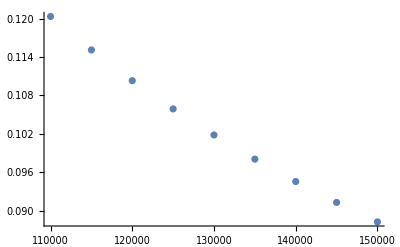

```mathematica
ListPlot[Table[{x,-U[x][[82]]},{x,110000,150000, 5000}]]
```

```mathematica
-U[1.32 10^5][[82]]
```

0.100286

```mathematica
-U[1.47 10^5][[82]]
```

0.0900523

```mathematica
-U[1.20 10^5][[82]]
```

0.110314

```mathematica
1.47-1.32
1.32-1.20
```

0.15

0.12

```mathematica
(0.15+0.12)/2
```

0.135

### Acceptance-rejection sampling

```mathematica
p[x_]:=PDF[NormalDistribution[10^5,2 10^4],x];
pd[x_]:=PDF[NormalDistribution[1.32 10^5,0.135 10^5],x];
likelih[x_]:=pd[x] p[x];
```

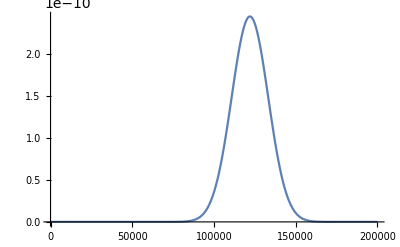

```mathematica
Plot[likelih[x],{x,0,2 10^5},PlotRange->Full]
```

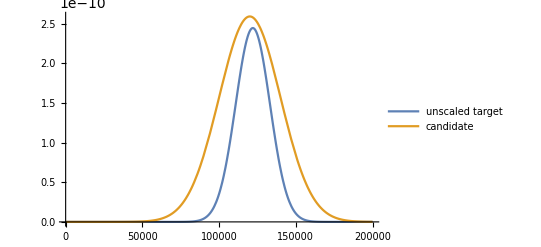

```mathematica
g[x_]:=PDF[NormalDistribution[1.2 10^5,0.2 10^5],x];
M=  1.3 10^(-5);
Plot[{likelih[x],M g[x]},{x,0,2 10^5},PlotRange->Full,PlotLegends->{"unscaled target","candidate"}]
```

```mathematica
posterior={};
For[i=1,i<100000,i++,
x=RandomVariate[NormalDistribution[1.2 10^5,0.2 10^5]];
w= pd[x]p[x]/(M g[x]);
u=RandomVariate[UniformDistribution[{0,1}]];
If[u<w,AppendTo[posterior,x]]
]
```

#### The posterior pdf

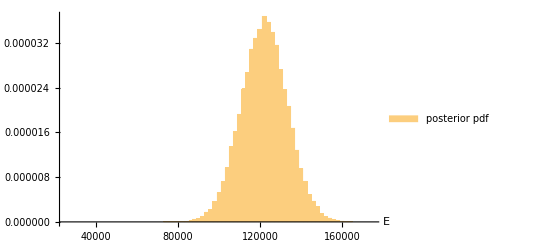

```mathematica
hist=Histogram[posterior,{0.25 10^5, 1.75 10^5,2000},"PDF",AxesLabel->{"E"},ChartLegends->{"posterior pdf"}]
```

#### The prior pdf

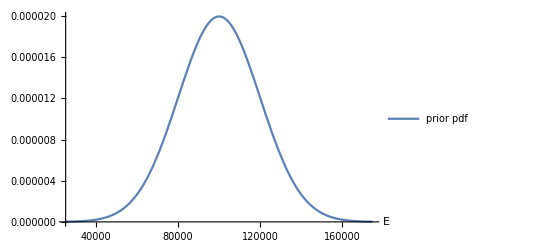

```mathematica
plot = Plot[p[x],{x,0.25 10^5, 1.75 10^5},AxesLabel->{"E"},PlotLegends->{"prior pdf"}]
```

#### Comparison

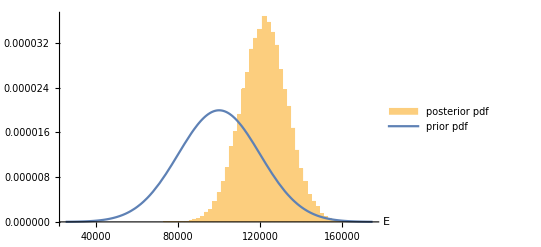

```mathematica
Show[hist,plot]
```